```mathematica
(*This is for Fig 5*)
(*Initialization*)
ClearAll["Global`*"]
```

```mathematica
(*define the function for computing Λ*)
A0=-0.3; (*A0=ρbar/2*)
Λvalue[γ_,A_,ω_,q_]:=Module[{T,sol1,sol2,Λp,Λn},T=2π/ω;sol1=NDSolve[{Rt2'[x]+q/2(A0+A Cos[ω x]) -2 It2[x]q(1+A0+A Cos[ω x])-Rt2[x]q γ(1+Cos[ω x])/2-2(Rt2[x]^2-It2[x]^2)q (A0+A Cos[ω x])==0,It2'[x]+2 Rt2[x]q(1+A0+A Cos[ω x])-It2[x]q γ(1+Cos[ω x])/2- 4(Rt2[x]It2[x]) q (A0+A Cos[ω x])==0,Rt2[0]==Rt2[T],It2[0]==It2[T]},{Rt2,It2},{x,0,2T}];
sol2=NDSolve[{Rs2'[x]+q/2(A0+A Cos[ω x])-2 Is2[x]q(1+A0+A Cos[ω x])+Rs2[x]q γ(1+Cos[ω x])/2-2(Rs2[x]^2-Is2[x]^2)q (A0+A Cos[ω x])==0,Is2'[x]+2 Rs2[x]q(1+A0+A Cos[ω x])+Is2[x]q γ(1+Cos[ω x])/2- 4(Rs2[x]Is2[x]) q (A0+A Cos[ω x])==0,Rs2[0]==Rs2[T],Is2[0]==Is2[T]},{Rs2[x],Is2[x]},{x,0,2T}];Λn=(1+A0)-γ/(4I)+(2I)/T NIntegrate[(A0+A Cos[ω x])Evaluate[Rt2[x]]/.sol1[[1]][[1]],{x,0,T}]-2/T NIntegrate[(A0+A Cos[ω x])Evaluate[It2[x]]/.sol1[[1]][[2]],{x,0,T}];
Λp=(1+A0)+γ/(4I)+(2I)/T NIntegrate[(A0+A Cos[ω x])Evaluate[Rs2[x]]/.sol2[[1]][[1]],{x,0,T}]-2/T NIntegrate[(A0+A Cos[ω x])Evaluate[Is2[x]]/.sol2[[1]][[2]],{x,0,T}];{Λn,Λp}];
```

```mathematica
(*the normal instability*)
{Λn,Λp}=Λvalue[0.13,0.15,1.25,1]
γ=0.13;
(*right movers*)
spectrumR=Flatten[Table[I(Λn+Λp)(m1-n1)/2-γ(m1+n1)/4-I(Λp-Λn)(m1+n1)/2,{m1,0,10},{n1,0,10}]];
data=Transpose[{Re[spectrumR],Im[spectrumR]}];
ListPlot[{Style[#,RGBColor["#1A80BB"]]&/@Select[data,#[[1]]<=0&],Style[#,RGBColor["#F0785E"]]&/@Select[data,#[[1]]>0&]},
PlotRange->Full,AspectRatio->0.75,
Axes->None,
Epilog->{{Black,Dashed,Line[{{0,7},{0,-7}}]},{Black,Dashed,Line[{{-3,0},{2,0}}]}},
PlotStyle->{PointSize[0.013]},
FrameTicks->{{Range[-6,6,2],None},{Range[-2,2,0.5],None}},
FrameStyle->Directive[Black,15],
Frame->True]
(*left movers*)
spectrumL=Flatten[Table[I(Λn+Λp)(m2-n2)/2-γ(m2+n2)/4-I(Λp-Λn)(-m2-n2)/2,{m2,0,10},{n2, 0,10}]];
data=Transpose[{Re[spectrumL],Im[spectrumL]}];
ListPlot[{Style[#,RGBColor["#1A80BB"]]&/@Select[data,#[[1]]<=0&],Style[#,RGBColor["#F0785E"]]&/@Select[data,#[[1]]>0&]},
PlotRange->Full,AspectRatio->0.75,
Axes->None,
Epilog->{{Black,Dashed,Line[{{0,7},{0,-7}}]},{Black,Dashed,Line[{{-3,0},{2,0}}]}},
PlotStyle->{PointSize[0.013]},
FrameTicks->{{Range[-6,6,2],None},{Range[-2,2,0.5],None}},
FrameStyle->Directive[Black,15],
Frame->True]
```

{0.628318-0.122371 ⅈ,0.621682-0.122371 ⅈ}

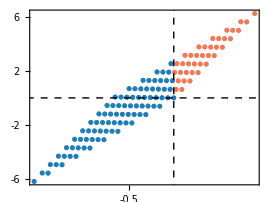

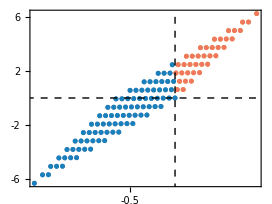

{0.62146+0.123243 ⅈ,0.62146-0.123243 ⅈ}

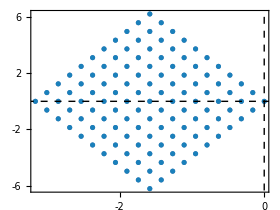

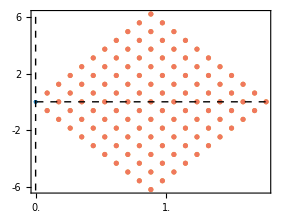

```mathematica
(*the chiral instability*)
{Λn,Λp}=Λvalue[0.14,0.15,1.25,1]
γ=0.14;
(*right movers*)
spectrumR=Flatten[Table[I(Λn+Λp)(m1-n1)/2-γ(m1+n1)/4-I(Λp-Λn)(m1+n1)/2,{m1,0,10},{n1,0,10}]];
data=Transpose[{Re[spectrumR],Im[spectrumR]}];
ListPlot[DeleteCases[{Style[#,RGBColor["#1A80BB"]]&/@Select[data,#[[1]]<=0&],Style[#,RGBColor["#F0785E"]]&/@Select[data,#[[1]]>0&]},{}],
PlotRange->Full,AspectRatio->0.75,
Axes->None,
Epilog->{{Black,Dashed,Line[{{0,7},{0,-7}}]},{Black,Dashed,Line[{{-6,0},{0.1,0}}]}},
PlotStyle->{PointSize[0.013]},
FrameTicks->{{Range[-6,6,2],None},{Range[-6,0,1],None}},
FrameStyle->Directive[Black,15],
Frame->True]
(*left movers*)
spectrumL=Flatten[Table[I(Λn+Λp)(m2-n2)/2-γ(m2+n2)/4-I(Λp-Λn)(-m2-n2)/2,{m2,0,10},{n2, 0,10}]];
data =Transpose[{Re[spectrumL],Im[spectrumL]}];
ListPlot[{Style[#,RGBColor["#1A80BB"]]&/@Select[data,#[[1]]<=0&],Style[#,RGBColor["#F0785E"]]&/@Select[data,#[[1]]>0&]},
PlotRange->Full,AspectRatio->0.75,
Axes->None,
Epilog->{{Black,Dashed,Line[{{0,7},{0,-7}}]},{Black,Dashed,Line[{{-0.1,0},{3,0}}]}},
PlotStyle->{RGBColor["#1A80BB"],PointSize[0.013]},
FrameTicks->{{Range[-6,6,2],None},{Range[0,2.5,0.5],None}},
FrameStyle->Directive[Black,15],
Frame->True]
```